```mathematica
tick[n_]:=(1+Cos[π n])/2
```

```mathematica
tock[n_]:=1-tick[n]
```

```mathematica
even[n_]:=n/2
```

```mathematica
odd[n_]:=3n+1
```

```mathematica
co[n_]:=tick[n]even[n]+tock[n]odd[n]
```

```mathematica
co[n]
```

(1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])

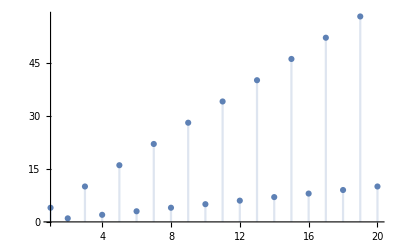

```mathematica
DiscretePlot[(1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]),{n,1,20}]
```

```mathematica
Nest[f,x,n]==Nest[f,x,n+1]
```

Nest::intnm: Non-negative machine-sized integer expected at position 3 in Nest[f,x,n].

Nest::intnm: Non-negative machine-sized integer expected at position 3 in Nest[f,x,1+n].

Nest[f,x,n]==Nest[f,x,1+n]

```mathematica
col[111]
```

col[111]

```mathematica
co[111]
```

334

```mathematica
collate[1]=2
```

2

```mathematica
collate[533]
```

collate[533]

```mathematica
collate[1]
```

2

```mathematica
Do[collate[i]=co[i],{i,1,100}]
```

```mathematica
2
```

2

```mathematica
ClearAll[collate]
```

```mathematica
Table[i->co[i],{i,1,20}]
```

{1→4,2→1,3→10,4→2,5→16,6→3,7→22,8→4,9→28,10→5,11→34,12→6,13→40,14→7,15→46,16→8,17→52,18→9,19→58,20→10}

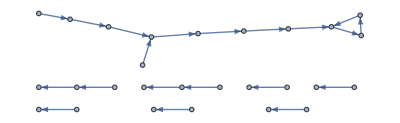

```mathematica
Graph[{1->4,2->1,3->10,4->2,5->16,6->3,7->22,8->4,9->28,10->5,11->34,12->6,13->40,14->7,15->46,16->8,17->52,18->9,19->58,20->10}]
```

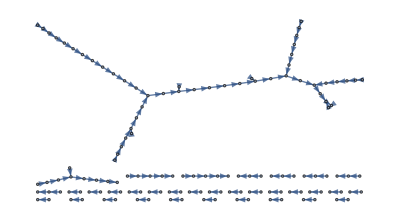

```mathematica
Graph[
Table[i->co[i],{i,1,100}]
]
```

```mathematica
colcount[n_]:=Piecewise[{{1, n==1}, {colcount[co[n]]+1, n>1}}]
```

```mathematica
colcount[1]
```

1

```mathematica
colcount[2]
```

2

```mathematica
colcount[n_]:=Piecewise[{{1, n==1}, {colcount[co[n]], n>1}}]
```

```mathematica
colcount[2]
```

1

```mathematica
colcount[64]
```

1

```mathematica
colcount[n_]:=Piecewise[{{1, n==1}, {colcount[co[n]]+1, n>1}}]
```

```mathematica
colcount[8]
```

4

```mathematica
colcount[64]
```

7

```mathematica
Log[2,n-1]
```

Log[-1+n]/Log[2]

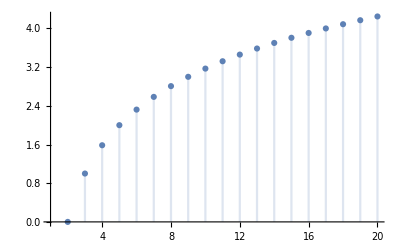

```mathematica
DiscretePlot[Log[-1+n]/Log[2],{n,1,20}]
```

```mathematica
colcount[101]
```

26

```mathematica
Nest[co,n,26]
```

$Aborted[]

```mathematica
Nest[co,101,26]
```